## Control Framework for Slung Load Transportation with Two Aerial Vehicles

# Notation

## some useful functions

```mathematica
(*Orthogonal Projection Operator*)
OP[x_]:=IdentityMatrix[3]-KroneckerProduct[x, x]
(*Skew symmetric matrix*)
Skew[ω_]:={{0,-ω[[3]],ω[[2]]},{ω[[3]],0,-ω[[1]]},{-ω[[2]],ω[[1]],0}}
```

```mathematica
(*Parametrization of unit vector with psi and theta angle*)
(*uv1[{0,0}] = e1 -- first canonical basis vector*)
uv1[θ_]:={Cos[θ[[2]]]Cos[θ[[1]]],Cos[θ[[2]]]Sin[θ[[1]]],-Sin[θ[[2]]]}
(*uv3[{0,0}] = e3 -- third canonical basis vector*)
uv3[θ_]:={Cos[θ[[2]]] Sin[θ[[1]]],Sin[θ[[2]]],Cos[θ[[1]]] Cos[θ[[2]]]}

(*'derivative'*)
Duv1[θ_,ω_]:=(D[uv1[{θ1,θ2}],{{θ1,θ2}}].ω)/.Thread[{θ1,θ2}-> θ]
Duv3[θ_,ω_]:=(D[uv3[{θ1,θ2}],{{θ1,θ2}}].ω)/.Thread[{θ1,θ2}-> θ]
```

# Modeling and Problem Statement

## Some definitions: these are dummy names for state and input

```mathematica
(*kinematic variables*)
p={px,py,pz};
P1={p1x,p1y,p1z};
P2={p2x,p2y,p2z};
zk=Join[p,P1,P2];

(*dynamic variables*)
v={vx,vy,vz};
V1={v1x,v1y,v1z};
V2={v2x,v2y,v2z};
zd=Join[v,V1,V2];
z=Join[zk,zd];

(*input variable*)
u1={u1x,u1y,u1z};
u2={u2x,u2y,u2z};
u=Join[u1,u2];
```

## physical constants

```mathematica
(*Set some random parameters*)
PhysicalConstants ={
gravity-> 9.81,
m-> 0.5,
L1-> 0.5,L2-> 0.7,
m1-> 1.4,m2-> 2.0,
w1-> 0.4,w2-> 0.6};
```

choose ration of weights (w1,w2) to be equal to ratio of vehicle masses (this is a choice: other choices are possible)

#### this means heavier vehicle will carry more load than lighter one

```mathematica
w1/w2/.PhysicalConstants
m1/m2/.PhysicalConstants
```

0.666667

0.7

## state space

```mathematica
ZSET[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=
{
((#.# - L1^2)&)[P1-p],
((#.# - L2^2)&)[P2-p],
(#1.#2 &)[P1-p,V1-v],
(#1.#2 &)[P2-p,V2-v]
};
```

## map that generates any point in state space domain

```mathematica
zl[l_]:=Join[
l[[1;;3]],
l[[1;;3]]+L1 uv3[l[[4;;5]]],
l[[1;;3]]+L2 uv3[l[[6;;7]]],
l[[8;;10]],
l[[8;;10]]+L1 Duv3[l[[4;;5]],l[[11;;12]]],
l[[8;;10]]+L2 Duv3[l[[6;;7]],l[[13;;14]]]
]/.PhysicalConstants

(*random point*)
zlR[]:=zl[RandomReal[{-1,1},14]]
zlR[]
```

{0.0191406,-0.859928,-0.236324,0.249771,-0.476843,-0.0125931,-0.236558,-1.3322,0.212646,0.967,-0.549304,-0.145614,1.01397,-0.388439,-0.469479,1.24781,-0.574315,-0.0119935}

## verify that point from previous map does belong to state space

```mathematica
Chop[ZSET[zlR[]]/.PhysicalConstants]//Simplify
```

{0,0,0,0}

## tangent set

```mathematica
δp={δpx,δpy,δpz};δP1={δp1x,δp1y,δp1z};δP2={δp2x,δp2y,δp2z};
δv={δvx,δvy,δvz};δV1={δv1x,δv1y,δv1z};δV2={δv2x,δv2y,δv2z};
TangentZSET[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},
{δpx_,δpy_,δpz_,δp1x_,δp1y_,δp1z_,δp2x_,δp2y_,δp2z_,δvx_,δvy_,δvz_,δv1x_,δv1y_,δv1z_,δv2x_,δv2y_,δv2z_}
]={
(#1.#2 &)[P1-p,δP1-δp],
(#1.#2&)[P2-p,δP2-δp],
(#3.#2+#1.#4 &)[P1-p,V1-v,δP1-δp,δV1-δv],
(#3.#2+#1.#4 &)[P2-p,V2-v,δP2-δp,δV2-δv]
};
```

## vector field

```mathematica
(*cables' unit vectors and agular velocities*)
n1[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=(P1-p)/L1;
n2[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=(P2-p)/L2;
ω1[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Skew[(P1-p)/L1].((V1-v)/L1);
ω2[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Skew[(P2-p)/L2].((V2-v)/L2);


(*defining quatities necessary for computing tension in cables*)
MT[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=(DiagonalMatrix[{m/m1,m/m2}]+{{1,γ},{γ,1}})/.{γ-> n1[zk].n2[zk]};

B[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]={
n1[zk].((m u1)/m1)+m/L1(V1-v).(V1-v),
n2[zk].((m u2)/m2)+m/L2(V2-v).(V2-v)};

MTinv[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=1/((m (m + m1 +m2))/(m1 m2)+1-γ^2){{1+m/m2,- γ},{- γ,1+m/m1}}/.{γ-> n1[zk].n2[zk]};
Tensions[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=MTinv[zk].B[z,u];
```

### accelerations (of load, and uavs)

```mathematica
a[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=1/m(T1 n1[zk]+T2 n2[zk]- m gravity {0,0,1})/.Thread[{T1,T2}-> Tensions[z,u]];

A1[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]= 1/m1(u1-T1 n1[zk]- m1 gravity {0,0,1})/.Thread[{T1,T2}-> Tensions[z,u]];
A2[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]= 1/m2(u2-T2 n2[zk]- m2 gravity{0,0,1})/.Thread[{T1,T2}-> Tensions[z,u]];


(*complete vector field*)
Zk[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Join[v,V1,V2];
Zd[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=Join[a[z,u],A1[z,u],A2[z,u]]/.PhysicalConstants;
Z[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=Join[Zk[z],Zd[z,u]];

ZdFree[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Zd[z,{0,0,0,0,0,0}];

Z[zlR[],RandomReal[{-1,1},6]]
```

{0.661701,-0.857854,0.478111,0.757332,-0.945786,0.463158,0.414394,-1.35014,0.819286,-0.153785,-0.191808,-9.60234,-0.449964,0.177241,-9.50154,-0.389707,-0.208659,-10.2184}

## verify that vector field lives in tangent set

```mathematica
Chop[TangentZSET[z,Z[z,u]]/.PhysicalConstants/.Thread[z-> zlR[]]/.Thread[u-> RandomReal[{-1,1},6]]]
```

{0,0,0,0}

## verify that Zd = A + B U (input affine)

```mathematica
T1U[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Join[({1,0}.MTinv[zk].{1,0} m/m1)n1[zk],({1,0}.MTinv[zk].{0,1} m/m2)n2[zk]];
T2U[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Join[({0,1}.MTinv[zk].{1,0} m/m1)n1[zk],({0,1}.MTinv[zk].{0,1} m/m2)n2[zk]];
BA[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=KroneckerProduct[n1[zk]/m,T1U[zk]]+KroneckerProduct[n2[zk]/m,T2U[zk]];
BA1[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=1/m1 Join[IdentityMatrix[3],0IdentityMatrix[3],2]-KroneckerProduct[n1[zk]/m1,T1U[zk]];
BA2[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=1/m2 Join[0IdentityMatrix[3],IdentityMatrix[3],2]-KroneckerProduct[n2[zk]/m2,T2U[zk]];
BU[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Join[BA[zk],BA1[zk],BA2[zk]]/.PhysicalConstants;

error[z_,u_]:= Zd[z,u]-(Zd[z,{0,0,0,0,0,0}]+BU[z[[1;;9]]].u)
Chop[error[zlR[],RandomReal[{-1,1},6]]]
```

{0,0,0,0,0,0,0,0,0}

# Control Law Design: Control Strategy

## see companion pdf

# Control Law Design: Preliminary Definitions

## some necessary definitions

## From function f: Zk → Some Set, compute its velocity and acceleration (along vector field)

```mathematica
(*velocity*)
vf[f_]:=Evaluate[D[f[zk],{zk}].zd]/.Thread[zk-> #1]/.Thread[zd-> #2]&
(*acceleration = Af + Bf.u*)
Bf[f_]:=Evaluate[D[f[zk],{zk}]].BU[zk]/.Thread[zk-> #1]&
Af[f_]:=Evaluate[D[f[zk],{zk}].Zd[z,{0,0,0,0,0,0}]+D[vf[f][zk,zd],{zk}].zd]/.Thread[Join[zk,zd]-> #1]/.Thread[z-> #1]&
```

## unit vector, its angular velocity, and its angular acceleration from p, ṗ and p^(..)

```mathematica
npva[p_]:=p/(√(p.p))
ωpva[p_,v_]:=Skew[p/(√(p.p))].(v/(√(p.p)))
τpva[p_,v_,a_]:=Skew[p/(√(p.p))].(a/(√(p.p))-2 1/(√(p.p))^3(v.p)v )
```

## Unit vector from function f (and its angular velocity and acceleration)

```mathematica
nf[f_]:=npva[f[zk]]/.Thread[zk-> #1]&
ωf[f_]:=ωpva [f[zk],vf[f][zk,zd]]/.Thread[zk-> #1]/.Thread[zd-> #2]&
(*τf[f_]:=τpva[f[zk],vf[f][zk,zd],*acceleration*]*)
Bτf[f_]:=Skew[f[zk]/(√(f[zk].f[zk]))].((Bf[f][zk])/(√(f[zk].f[zk])))/.Thread[zk-> #1]&
Aτf[f_]:= τpva[f[zk],vf[f][zk,zd],Af[f][z]]/.Thread[Join[zk,zd]-> #1]/.Thread[z-> #1]&
```

## Functions that we wish to control

### Function NT (vector that will be thrust vector)

```mathematica
(*ωT[x_]:=ωf[NT][zk[x],xd[x]]*)
NT[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=w1 n1[zk]+w2 n2[zk]/.PhysicalConstants;
nT[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=npva[NT[zk]];
(*ωT[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=ωpva[NT][zk,zd]/.PhysicalConstants;*)
ωT[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_},{vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Skew[nT[zk]].(w1 (V1-v)/L1+w2 (V2-v)/L2)1/(√(NT[zk].NT[zk]))/.PhysicalConstants;
BτNT[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Bτf[NT][zk];
AτNT[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Aτf[NT][z];

(*ωT[#[[1;;9]],#[[10;;18]]]&[zlR[]]*)
(*BτNT[zlR[][[1;;9]]]*)
(*AτNT[zlR[]]*)
```

### Function θ (angle between cables)

```mathematica
θ[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=ArcCos[n1[zk].n2[zk]]/.PhysicalConstants;
ωθ[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_},{vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=vf[θ][zk,zd];
Bθ[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Bf[θ][zk];
Aθ[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Af[θ][z];

(*ωθ[#[[1;;9]],#[[10;;18]]]&[zlR[]]*)
(*Bθ[zlR[][[1;;9]]]*)
(*Aθ[zlR[]]*)
```

### Function ψ (‘yaw angle’)

```mathematica
NH[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=OP[{0,0,1}].(n1[zk]-n2[zk])/.PhysicalConstants;
nH[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=npva[NH[zk]/(√(NH[zk].NH[zk]))];
(*''Alternative''*)
(*ψ[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=ArcTan[{1,0,0}.nH[zk],{0,1,0}.nH[zk]];*)
ψ[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=1/2 ArcTan[({1,0,0}.nH[zk])^2-({0,1,0}.nH[zk])^2,2({1,0,0}.nH[zk])({0,1,0}.nH[zk])];
ωψ[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_},{vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=vf[ψ][zk,zd];
Bψ[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Bf[ψ][zk];
Aψ[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Af[ψ][z];

ωψ[#[[1;;9]],#[[10;;18]]]&[zlR[]]
Bψ[zlR[][[1;;9]]]
Aψ[zlR[]]
```

0.594705

{1.17039,0.384658,0.0158725,-0.582945,-0.200003,-0.00101871}

-0.509802

### some small test (check ‘’derivative’’ functions are well computed)

```mathematica
test[zz_,u_]:=(D[ψ[zk],{zk}]/.Thread[z-> zz]).(Z[zz,u][[1;;9]]) -(ωψ[zz[[1;;9]],zz[[10;;18]]])
Chop[test[zlR[],RandomReal[{-1,1},6]]]
test[zz_,u_]:=(D[ωψ[zk,zd],{z}]/.Thread[z-> zz]).Z[zz,u] -(Bψ[zz[[1;;9]]].u + Aψ[zz])
Chop[test[zlR[],RandomReal[{-1,1},6]]]
```

0

0

# Control Law Design: Input Transformation

## Matrix A and B of function R we wish to control

```mathematica
RB[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Join[
1/m(KroneckerProduct[n1[zk],T1U[zk]]+KroneckerProduct[n2[zk],T2U[zk]]),(*control thrust of load*)
BτNT[zk],(*control torque of thrust vector, i.e, of nT*)
{Bθ[zk],Bψ[zk]}(*control θ and ψ*)
]/.PhysicalConstants;
(*N[RB[zlR[][[1;;9]]]]//MatrixForm*)
(*PseudoInverse[N[RB[zlR[][[1;;9]]] ]]//MatrixForm*)
```

```mathematica
RA[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Join[1/m(n1[zk]T10+n2[zk]T20),AτNT[z],{Aθ[z]},{Aψ[z]}]/.Thread[{T10,T20}-> Tensions[z,{0,0,0,0,0,0}]]/.PhysicalConstants;
(*N[RA[zlR[]] ]//MatrixForm*)
```

## Input transformation

```mathematica
ubar[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]:=PseudoInverse[RB[{px,py,pz,p1x,p1y,p1z,p2x,p2y,p2z}]].(
Join[ T nT[{px,py,pz,p1x,p1y,p1z,p2x,p2y,p2z}] ,{τx,τy,τz},{τθ,τψ}] -
RA[{px,py,pz,p1x,p1y,p1z,p2x,p2y,p2z,vx,vy,vz,v1x,v1y,v1z,v2x,v2y,v2z}]
)/.PhysicalConstants;
Timing[ubar[zlR[],RandomReal[{-10,10},6]]]
```

{0.14,{-10.5444,11.9149,-0.473602,-15.284,7.67859,4.23722}}

## Check that input transformation is indeed well defined in domain defined in article

```mathematica
uv=#/(√(#.#))&;

ubar1st[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},T_]=Join[u1x n1[zk],u2x n2[zk]]/.Thread[{u1x,u2x}-> DiagonalMatrix[{m1/m,m2/m}].MT[zk].((m T)/(√(NT[zk].NT[zk])){ w1 ,w2}-Tensions[z,{0,0,0,0,0,0}])]/.PhysicalConstants;

ubar2nd[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=ubar1st[z,T]+Join[
((L1 m1)/w1(τψ+√(NT[zk].NT[zk])1/2{ττx,ττy,ττz}.uv[OP[nT[zk]].n1[zk]])uv[Skew[n1[zk]].nT[zk]]-(L1 m1)/w1(1/(n1[zk].nT[zk])τθ+(NT[zk].NT[zk])/((w1 +w2)(1+ n1[zk].n2[zk])){ττx,ττy,ττz}.uv[Skew[nT[zk]].n1[zk]])uv[OP[n1[zk]].nT[zk]]),
((L2 m2)/w2(τψ+√(NT[zk].NT[zk])1/2{ττx,ττy,ττz}.uv[OP[nT[zk]].n2[zk]])uv[Skew[n2[zk]].nT[zk]]-(L2 m2)/w2(1/(n2[zk].nT[zk])τθ+(NT[zk].NT[zk])/((w1 +w2)(1+ n1[zk].n2[zk])){ττx,ττy,ττz}.uv[Skew[nT[zk]].n2[zk]])uv[OP[n2[zk]].nT[zk]])
]/.Thread[{ττx,ττy,ττz}-> {τx,τy,τz}-(AτNT[z]+BτNT[zk].ubar1st[z,T]) ]/.PhysicalConstants;

ubar3rd[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=ubar2nd[z,{T,τx,τy,τz,ττθ,τψ}]/.{ττθ-> ((w2^2 + w1 w2 n1[zk].n2[zk])(w1^2 +w1 w2 n1[zk].n2[zk]))/(√(NT[zk].NT[zk]))^3(τθ-(Aθ[z]+Bθ[zk].ubar2nd[z,{T,τx,τy,τz,0,0}]))}/.PhysicalConstants;

ubar4th[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=ubar3rd[z,{T,τx,τy,τz,τθ,ττψ}]/.{ττψ->(NH[zk].NH[zk] √(1-(n1[zk].n2[zk])^2))/((1/w1+1/w2)({0,0,1}.n1[zk]+{0,0,1}.n2[zk])(n1[zk].n2[zk]-1))(τψ-(Aψ[z]+Bψ[zk].Evaluate[ubar3rd[z,{T,τx,τy,τz,τθ,0}]]))}/.PhysicalConstants;
```

```mathematica
zrandom=zlR[];
(*test[{T_,τx_,τy_,τz_,τθ_,τψ_}]:=Join[m T nT[#1[[1;;9]]] ,OP[nT[#1[[1;;9]]]].{τx,τy,τz},{τθ,τψ}]-(RA[#1]+RB[#1[[1;;9]]].ubar1st[#1,T]) &[zrandom]/.PhysicalConstants;*)
(*test[{T_,τx_,τy_,τz_,τθ_,τψ_}]:=Join[m T nT[#1[[1;;9]]] ,OP[nT[#1[[1;;9]]]].{τx,τy,τz},{τθ,τψ}]-(RA[#1]+RB[#1[[1;;9]]].ubar2nd[#1,{T,τx,τy,τz,τθ,τψ}]) &[zrandom]/.PhysicalConstants;*)
(*test[{T_,τx_,τy_,τz_,τθ_,τψ_}]:=Join[m T nT[#1[[1;;9]]] ,OP[nT[#1[[1;;9]]]].{τx,τy,τz},{τθ,τψ}]-(RA[#1]+RB[#1[[1;;9]]].ubar3rd[#1,{T,τx,τy,τz,τθ,τψ}]) &[zrandom]/.PhysicalConstants;*)
test[{T_,τx_,τy_,τz_,τθ_,τψ_}]:=Join[ T nT[#1[[1;;9]]] ,OP[nT[#1[[1;;9]]]].{τx,τy,τz},{τθ,τψ}]-(RA[#1]+RB[#1[[1;;9]]].ubar4th[#1,{T,τx,τy,τz,τθ,τψ}]) &[zrandom]/.PhysicalConstants;
Timing[Chop[test[RandomReal[{-1,1},6]]]]
```

{3.46,{0,0,0,0,0,0,0,0}}

## check they match indeed

```mathematica
Timing[Chop[ubar[#1,#2]-ubar4th[#1,#2] &[zrandom,RandomReal[{-1,1},6]]/.PhysicalConstants]]
```

{3.496,{0,0,0,0,0,0}}

# Control Law Design: State Transformation

```mathematica
g[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Join[
p,v,nT[zk],ωT[zk,zd],(*position, velocity, unit vector and angular velocity of thrust propelled system*)
{θ[zk],ωθ[zk,zd]},(*theta and theta dot: angle between cables is double integrator*)
{ψ[zk],ωψ[zk,zd]}(*yaw and yaw dot: yaw position is double integrator*)
]/.PhysicalConstants;
(*N[g[zlR[]]]*)
```

## generator element in codomain of g (X state space)

```mathematica
positive3rd={#[[1]],#[[2]],Abs[#[[3]]]}&;
xl[l_]:=Join[
l[[1;;3]],
l[[4;;6]],
positive3rd[uv3[l[[7;;8]]]],
 Skew[positive3rd[uv3[l[[7;;8]]]]].Duv3[l[[7;;8]],l[[9;;10]]],
{
Min[{π-ϵps,Max[{0+ϵps,l[[11]]}]}],(*we require that theta in [0,pi]*)
l[[12]],
Min[{π/4-ϵps,Max[{-π/4+ϵps,l[[13]]}]}],l[[14]](*we require that yaw in [-π/4,π/4]: this can be lifted tough*)
}
]/.{ϵps-> 0.001}/.PhysicalConstants

xlR[]:=xl[RandomReal[{-1,1},14]]
xlR[]
```

{-0.393433,-0.654368,0.467344,-0.913877,-0.682885,-0.447469,0.429839,-0.839369,0.332712,-0.315309,0.0344348,0.494228,0.846317,-0.540889,0.434249,0.625225}

## inverse of map g

```mathematica
(*let's postulate solution of this form*)
n1sol={a1,b1,√(1-a1^2-b1^2)};
n2sol={a2,b2,√(1-a2^2-b2^2)};

(*ArcTan[#[[1]],#[[2]]]&[OP[{0,0,1}].(n1sol-n2sol)]//Simplify*)
(*sol1=(2 #[[2]]#[[1]])/((#[[1]])^2-(#[[2]])^2)&[#&[OP[{0,0,1}].(n1sol-n2sol)]]//Simplify(*(b1-b2)/(a2-a1) = Tan[ψ]*)*)
sol1=(#[[2]])/(#[[1]])&[OP[{0,0,1}].(n1sol-n2sol)]//Simplify(*(b1-b2)/(a2-a1) = Tan[ψ]*)
sol2=n1sol.n2sol//Simplify(*n1.n2 = Cos[θ]*)

(*nT = (w1 n1 + w2 n2)/Norm[w1 n1 + w2 n2]*)
sol3=FullSimplify[
(#[[1;;2]])/(√(#.#))&[w1 n1sol+w2 n2sol]
]
```

(b1-b2)/(a1-a2)

a1 a2+b1 b2+√(1-a1^2-b1^2) √(1-a2^2-b2^2)

{(a1 w1+a2 w2)/(√(w1^2+2 (a1 a2+b1 b2+√(1-a1^2-b1^2) √(1-a2^2-b2^2)) w1 w2+w2^2)),(b1 w1+b2 w2)/(√(w1^2+2 (a1 a2+b1 b2+√(1-a1^2-b1^2) √(1-a2^2-b2^2)) w1 w2+w2^2))}

denominator: w1^2+2 (a1 a2+b1 b2+√(1-a1^2-b1^2) √(1-a2^2-b2^2)) w1 w2+w2^2 = w1^2+w2^2+Cos[θ](see sol2)

```mathematica
sol2/.Thread[{a1,b1}-> {{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}}.{a1,b1}]/.Thread[{a2,b2}-> {{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}}.{a2,b2}]//Simplify
a1 w1+a2 w2-AA nTx/.Thread[{a1,b1}-> {{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}}.{a1,b1}]/.Thread[{a2,b2}-> {{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}}.{a2,b2}]/.Thread[{nTx,nTy}-> {{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}}.{nTx,nTy}]//Simplify
b1 w1 +b2 w2-AA nTy/.Thread[{a1,b1}-> {{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}}.{a1,b1}]/.Thread[{a2,b2}-> {{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}}.{a2,b2}]/.Thread[{nTx,nTy}-> {{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}}.{nTx,nTy}]//Simplify
```

a1 a2+b1 b2+√(1-a1^2-b1^2) √(1-a2^2-b2^2)

(-AA nTx+a1 w1+a2 w2) Cos[ψ]+(AA nTy-b1 w1-b2 w2) Sin[ψ]

(-AA nTy+b1 w1+b2 w2) Cos[ψ]+(-AA nTx+a1 w1+a2 w2) Sin[ψ]

```mathematica
(*sol=Simplify[
Solve[
{
(2 (a1-a2) (b1-b2))/((a1-a2)^2+(b1-b2)^2)==Tan[2 ψ],
sol2==Cos[θ],
a1 w1+a2 w2==SnTx,
b1 w1 +b2 w2==SnTy
},
{a1,a2,b1,b2}
], w1> 0 && w2 > 0 
];*)
```

```mathematica
sol=Simplify[
Solve[
{
b1==b2,(*Assume that b1 and b2 are equal*)
sol2==Cos[θ],
a1 w1+a2 w2==√(w1^2+w2^2+2 w1 w2 Cos[θ])nTx,
b1 w1 +b2 w2==√(w1^2+w2^2+2 w1 w2 Cos[θ])nTy
},
{a1,a2,b1,b2}
], w1> 0 && w2 > 0 
];
```

### solution 2 is the correct because, we want a1>a2

```mathematica
(*a1-a2/.sol[[1]]//Simplify*)
(*a1-a2/.sol[[2]]//Simplify*)
```

```mathematica
Simplify[(a1-a2)-((√(w1^2+w2^2+2 w1 w2 Cos[θ]))/((1-nTy^2) (w1+w2) (w1^2+w2^2+2 w1 w2 Cos[θ]))(w1+w2)(nTx (1- Cos[θ])(w1-w2)+  √(((w1-w2)^2 (Cos[θ]+1-2 nTy^2 ) +4 w1 w2 (1- nTy^2)(1+Cos[θ])) (1-Cos[θ])(1-nTx^2-nTy^2))))/.sol[[2]],w1^2+w2^2+2 w1 w2 Cos[θ]>0]
Simplify[(a1-a2)-((√(w1^2+w2^2+2 w1 w2 Cos[θ]))/((1-nTy^2) (w1+w2) (w1^2+w2^2+2 w1 w2 Cos[θ]))(w1+w2)(nTx (1- Cos[θ])(w1-w2)-  √(((w1-w2)^2 (Cos[θ]+1-2 nTy^2 ) +4 w1 w2 (1- nTy^2)(1+Cos[θ])) (1-Cos[θ])(1-nTx^2-nTy^2))))/.sol[[1]],w1^2+w2^2+2 w1 w2 Cos[θ]>0]
```

0

0

### The latter for sol[[2]] is positive if (but not only if) nTz^2>π/4→ 1-2(nTz^2+nTy^2)>0!

```mathematica
(w1-w2)^2 (Cos[θ]+1-2 nTy^2 )(1-Cos[θ])(1-nTx^2-nTy^2)-(nTx (1- Cos[θ])(w1-w2))^2//Simplify
```

-2 (-1+nTy^2) (w1-w2)^2 (1-2 nTx^2-2 nTy^2+Cos[θ]) Sin[θ/2]^2

### We assume b1=b2: now we need to rotate by ψ, because b1 is not equal to b2

```mathematica
SOL=Thread[{a1,b1,a2,b2}-> (Join[#.{a1,b1},#.{a2,b2}]/.(sol[[2]]/.Thread[{nTx,nTy}->Transpose[#].{nTx,nTy}] ))]&[{{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}}];
random=Join[Thread[{w1,w2}-> RandomReal[{1,2},2]],Thread[{ψn,δn,ψ,θ}-> RandomReal[{-1,1},4]]];
```

### check solution satisfies conditions

```mathematica
Chop[((2 (a1-a2) (b1-b2))/((a1-a2)^2-(b1-b2)^2)-Tan[2 ψ])/.SOL/.{nTx-> Sin[δn]Cos[ψn],nTy-> Sin[δn]Sin[ψn]}/.random]
Chop[1/2 ArcTan[(a1-a2)^2-(b1-b2)^2,2 (a1-a2) (b1-b2)]- ψ/.SOL/.{nTx-> Sin[δn]Cos[ψn],nTy-> Sin[δn]Sin[ψn]}/.random]
Chop[((b1-b2)/(a1-a2)-Tan[ψ])/.SOL/.{nTx-> Sin[δn]Cos[ψn],nTy-> Sin[δn]Sin[ψn]}/.random]
Chop[(Cos[θ]-sol2)/.SOL/.{nTx-> Sin[δn]Cos[ψn],nTy-> Sin[δn]Sin[ψn]}/.random]
Chop[(a1 w1+a2 w2-√(w1^2+w2^2+2 w1 w2 Cos[θ])nTx)/.SOL/.{nTx-> Sin[δn]Cos[ψn],nTy-> Sin[δn]Sin[ψn]}/.random]
Chop[(b1 w1 +b2 w2-√(w1^2+w2^2+2 w1 w2 Cos[θ])nTy)/.SOL/.{nTx-> Sin[δn]Cos[ψn],nTy-> Sin[δn]Sin[ψn]}/.random]
```

0

0

0

«3 more identical outputs»

## Inverse map of g (call it h)

```mathematica
h[{px_,py_,pz_,vx_,vy_,vz_,nTx_,nTy_,nTz_,ωTx_,ωTy_,ωTz_,θ_,ωθ_,ψ_,ωψ_}]=Join[
{px,py,pz}(*p*),
{px,py,pz}+L1 n1sol/.SOL(*P1*),
{px,py,pz}+L2 n2sol/.SOL(*P2*),
{vx,vy,vz}(*v*),
{vx,vy,vz}+L1 Evaluate[D[n1sol/.SOL,{{ψ,θ,nTx,nTy}}]].{ωψ,ωθ,nTxD,nTyD}(*V1*),
{vx,vy,vz}+L2 Evaluate[D[n2sol/.SOL,{{ψ,θ,nTx,nTy}}]].{ωψ,ωθ,nTxD,nTyD}(*V2*)
]/.{nTxD ->  (-ωTz  nTy+ωTy  nTz),nTyD ->(ωTz  nTx-ωTx  nTz)}/.PhysicalConstants;

xrandom=xlR[];
Chop[#-g[h[#]]&[xrandom]]


zrandom= zlR[];
counter=1;
While[
!(-π/2<ArcTan[{1,0,0}.nH[zrandom[[1;;9]]],{0,1,0}.nH[zrandom[[1;;9]]]]<π/2 && n1[zrandom[[1;;9]]][[3]] >0&&n2[zrandom[[1;;9]]][[3]] >0)||counter≥10,
zrandom= zlR[];
(*Print["Not good point to test inverse"];*)
]
If[-π/4<ArcTan[{1,0,0}.nH[zrandom[[1;;9]]],{0,1,0}.nH[zrandom[[1;;9]]]]<π/4 && n1[zrandom[[1;;9]]][[3]] >0&&n2[zrandom[[1;;9]]][[3]] >0,
(*in constructing inverse, we took assumption the conditions above are satisfied*)
Print[Chop[#-h[g[#]]&[zrandom]]];
,
Print["Not good point to test inverse"];
Print[ψ[#]-ArcTan[{1,0,0}.nH[#],{0,1,0}.nH[#]]&[zrandom[[1;;9]]]];
]/.PhysicalConstants
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Not good point to test inverse

0.

```mathematica
(*h[{px_,py_,pz_,vx_,vy_,vz_,nTx_,nTy_,nTz_,ωTx_,ωTy_,ωTz_,θ_,ωθ_,ψ_,ωψ_}]=Join[
{px,py,pz}(*p*),
{px,py,pz}+L1 n1sol/.sol[[1]](*P1*),
{px,py,pz}+L2 n2sol/.sol[[1]](*P2*),
{vx,vy,vz}(*v*),
{vx,vy,vz}+L1 Evaluate[D[n1sol/.sol[[1]],{{ψ,θ,SnTx,SnTy}}]].{ωψ,ωθ,SnTxD,SnTyD}(*V1*),
{vx,vy,vz}+L2 Evaluate[D[n2sol/.sol[[1]],{{ψ,θ,SnTx,SnTy}}]].{ωψ,ωθ,SnTxD,SnTyD}(*V2*)
]/.{SnTx -> √(w1^2+w2^2+2 w1 w2 Cos[θ])nTx,SnTy -> √(w1^2+w2^2+2 w1 w2 Cos[θ])nTy}/.{SnTxD ->  (-2 w1 w2 Sin[θ] ωθ)/(2 √(w1^2+w2^2+2 w1 w2 Cos[θ]))nTx+ √(w1^2+w2^2+2 w1 w2 Cos[θ])(-ωTz  nTy+ωTy  nTz),SnTyD -> (-2 w1 w2 Sin[θ] ωθ)/(2 √(w1^2+w2^2+2 w1 w2 Cos[θ]))nTy+ √(w1^2+w2^2+2 w1 w2 Cos[θ])(ωTz  nTx-ωTx  nTz)}/.PhysicalConstants;
*)
```

## check dynamics in new coordinates without inverse

```mathematica
DynamicsEquality[zz_,{T_,τx_,τy_,τz_,τθ_,τψ_}]:=(
(D[g[z],{z}]/.Thread[z-> zz]).Z[zz,ubar[zz,{T,τx,τy,τz,τθ,τψ}]]-
Join[
zz[[10;;12]],
T nT[zz[[1;;9]]] - gravity{0,0,1},
Skew[ωT[zz[[1;;9]],zz[[10;;18]]]].nT[zz[[1;;9]]],
OP[nT[zz[[1;;9]]]].{τx,τy,τz},
{ωθ[zz[[1;;9]],zz[[10;;18]]],τθ},
{ωψ[zz[[1;;9]],zz[[10;;18]]],τψ}]
)/.PhysicalConstants
Chop[DynamicsEquality[zlR[],RandomReal[{-1,1},6]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Check dynamics equality with inverse (this is however not necessary)

```mathematica
DynamicsEquality[xx_,{T_,τx_,τy_,τz_,τθ_,τψ_}]:=(
(D[g[z],{z}].Z[h[xx],ubar[h[xx],{T,τx,τy,τz,τθ,τψ}]]/.Thread[z-> h[xx]])-
Join[
xx[[4;;6]],
T xx[[7;;9]] - gravity{0,0,1},
Skew[xx[[10;;12]]].xx[[7;;9]],
OP[xx[[7;;9]]].{τx,τy,τz},
{xx[[14]],τθ},
{xx[[16]],τψ}]
)/.PhysicalConstants
Chop[DynamicsEquality[xlR[],RandomReal[{-1,1},6]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

# Control Law Design: Separate control laws

## Desired trajectory

```mathematica
(*pd[t_]:={2 Cos[(2 3.142)/10 t],2Sin[(2 3.142)/10 t],0.5}*)
pd[t_]:={2 Cos[(2 3.142)/10 t],2Sin[(2 3.142)/10 t],0.5+0.3Sin[(2 3.142)/5 t]}
(*pd[t_]:={0,0,0}*)
```

## Controller for thrust propelled system

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"controller_thrust_propelled_system.m"}]]
(*gains of torque cascaded controller*)
BoundedDoubleIntegratorGains={kp-> 1.5,kv-> √2 √1.5,σp-> 0.6,σv-> 0.6,β-> 0.1};
AttitudeControllerGains={kp-> 3,kd-> √2 √3,kVp-> 100,kVd-> 200,β-> 0.1};

z3={0,0,0};
gravityfunction[t_]=pd''[t]+gravity {0,0,1}/.PhysicalConstants;
ControllerSubsystem1[t_,x1_]:=
ThrustPropelledController[
t,x1-Join[pd[t],pd'[t],{0,0,0},{0,0,0}],gravityfunction,
BoundedDoubleIntegratorGains,
(*{"PD" ,AttitudeControllerGains,{"Precise"},Null}*)
{"BackStepping",AttitudeControllerGains,{"Precise"},"on"}
];

v1cl[t_,x1_]:=ControllerSubsystem1[t,x1][[1]]
VV1[t_,x1_]:=ControllerSubsystem1[t,x1][[2]]
WW1[t_,x1_]:=ControllerSubsystem1[t,x1][[3]]
XX1[t_,x1_]:=ControllerSubsystem1[t,x1][[4]]
```

```mathematica
(*v1cl[0.1,{0,0,0,0,0,0,0,0,1,0,0,0}]*)
```

## Control law for theta

```mathematica
GainsThetaControl ={θeq -> π/6,kθp-> ωn^2,kθd-> 2 ξ ωn}/.{ωn-> 1.1,ξ-> 1};
uθcl[z_]:=-kθp (#θ-θeq)/(#θ(π/4-#θ))-kθd ωθ[z[[1;;9]],z[[10;;18]]]&[<|"θ"-> θ[z[[1;;9]]]|>]/.GainsThetaControl
(*uθcl[zlR[]]*)
```

NIntegrate::nlim: θ = α is not a valid limit of integration.

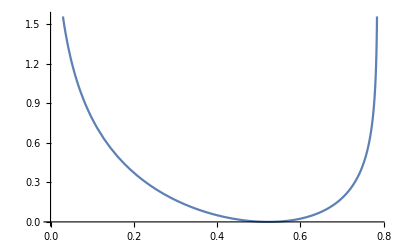

```mathematica
(*Simplify[Integrate[(θ-α)/(θ(π/4-θ)),{θ,α,θθ}],0<θθ<π/4]*)
Plot[NIntegrate[(θ-α)/(θ(π/4-θ)),{θ,α,θθ}]/.{α-> π/6},{θθ,0,π/4}]
```

## Control law for yaw

```mathematica
GainsYawControl ={kψp-> ωn^2,kψd-> 2 ξ ωn}/.{ωn-> 1.2,ξ-> 0.8};
uψcl[z_]:=-kψp Sin[2 ψ[z[[1;;9]]]]-kψd ωψ[z[[1;;9]],z[[10;;18]]]&[<|"θ"-> θ[z[[1;;9]]]|>]/.GainsYawControl
(*uψcl[zlR[]]*)
```

## Complete control law

```mathematica
ucl[t_,z_]:=ubar[z,Join[Flatten[v1cl[t,g[z][[1;;12]]]],{uθcl[z],uψcl[z]}]]
(*ucl[0.1,zlR[]]*)
```

just checking something

```mathematica
(*you may want to check this with: *)
(*pd[t_]:={0,0,0}*)
(*zspecial=Join[{0,0,0},L1{Sin[δ] Cos[ψψ],Sin[δ] Sin[ψψ],Cos[δ]},L2 {-Sin[δ] Cos[ψψ],-Sin[δ] Sin[ψψ],Cos[δ]},{0,0,0},{0,0,0},{0,0,0}]/.PhysicalConstants;*)
(*Chop[ucl[1, zspecial/.{δ-> 1/2 π/6}/.{ψψ-> π/2}]]*)
(*Chop[ucl[1, zspecial/.{δ-> 1/2 π/6}/.{ψψ-> π/2+0.00001}]]*)
(*Chop[ucl[1, zspecial/.{δ-> 1/2 π/6}/.{ψψ-> π/2-0.00001}]]*)
(*uψcl[ zspecial]//Simplify*)
```

## projection to guarantee that solution does not exit state set

```mathematica
Proj[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Join[
p,
p+L1 #/(√(#.#))&[P1-p] ,
p+L2 #/(√(#.#))&[P2-p],
v,
v+L1 OP[#/(√(#.#))].((V1-v)/(√(#.#)))&[P1-p],
v+L2 OP[#/(√(#.#))].((V2-v)/(√(#.#)))&[P2-p]
]/.PhysicalConstants;
Chop[# -Proj[#]&[zlR[]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*zrandom= zlR[];
counter=1;
While[
!(θ[zrandom[[1;;9]]]<π/4 )||counter≥10,
zrandom= zlR[];
(*Print["Not good point to test inverse"];*)
]
θ[zrandom[[1;;9]]] 180/π/.PhysicalConstants
ψ[zrandom[[1;;9]]] 180/π/.PhysicalConstants*)
```

## initial condition

```mathematica
z0=Join[{0,0,0},L1 uv3[{-0.1,-0.2}],L2 uv3[{0.2,0.4}],{0,0,0},{0,0,0},{0,0,0}]/.PhysicalConstants;
θ[z0[[1;;9]]] 180/π/.PhysicalConstants
ψ[z0[[1;;9]]] 180/π/.PhysicalConstants
ArcTan[{1,0,0}.nH[z0[[1;;9]]],{0,1,0}.nH[z0[[1;;9]]]] 180/π/.PhysicalConstants
```

38.2777

64.4741

-115.526

## Simulation

```mathematica
stepsize=0.01;
NN=1000;

stateList={};
inputList ={};
tensionsList={};
kk=1;

For[i=1,i<=NN,i++,
time=stepsize(i-1);
input =ucl[time,z0];
tensions= Tensions[z0,input]/.PhysicalConstants;

stateList= Join[stateList,{z0}];
inputList= Join[inputList,{input}];
tensionsList = Join[tensionsList,{tensions}];

zdot=  Z[z0,input]/.PhysicalConstants;
z0=Proj[z0+stepsize zdot]/.PhysicalConstants;

If[i≥100 kk,Beep[];Print[i];kk=kk+1];
]
```

100

200

300

400

500

600

700

800

900

1000

```mathematica
(*NN=Length[stateList]*)
```

```mathematica
XTicksLabels={{1,0},{200,2},{400,4},{600,6},{800,8},{1000,10}};
```

```mathematica
Export[NotebookDirectory[]<>"figures_no_attitude/matlab/data_state.mat",stateList];
Export[NotebookDirectory[]<>"figures_no_attitude/matlab/data_input.mat",inputList];
```

## Error position

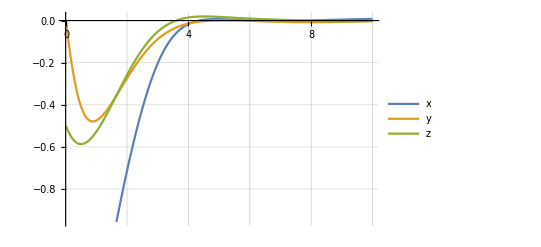
-Graphics-time (s)error(m)

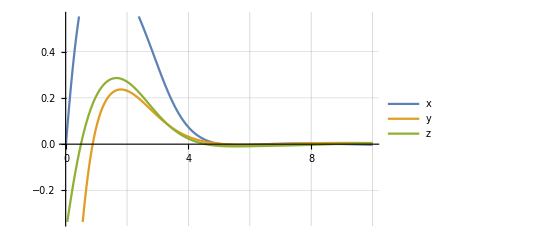
-Graphics-time (s)error(m/s)

```mathematica
errorp=stateList[[1;;NN,{1,2,3}]]-Table[pd[stepsize(i-1)],{i,1,NN}];
Labeled[
ListLinePlot[{
errorp[[;;,1]],
errorp[[;;,2]],
errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m)"},{Bottom,Left},RotateLabel->True
]

errorv=stateList[[1;;NN,{10,11,12}]]-Table[pd'[stepsize(i-1)],{i,1,NN}];
Labeled[
ListLinePlot[{
errorv[[;;,1]],
errorv[[;;,2]],
errorv[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m/s)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures_no_attitude/sim_error_position.pdf",%];
```

## Error attitude

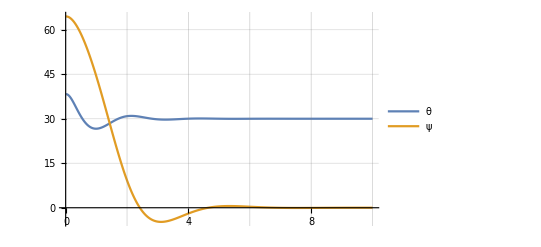
-Graphics-time (s)error(deg)

```mathematica
Labeled[
ListLinePlot[{
Table[θ[stateList[[i]][[1;;9]]] 180/π/.PhysicalConstants,{i,1,NN}],
Table[ψ[stateList[[i]][[1;;9]]] 180/π/.PhysicalConstants,{i,1,NN}],
(*Table[(ArcTan[{1,0,0}.nH[#],{0,1,0}.nH[#]]&[stateList[[i]][[1;;9]]] )180/π/.PhysicalConstants,{i,1,NN}]*)
},
PlotLegends->Placed[{"θ","ψ"},Above],
Ticks-> {XTicksLabels,Automatic},
PlotRange->Automatic,
GridLines->Automatic
],
{"time (s)","error(deg)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures_no_attitude/sim_error_attitude.pdf",%];
```

## Input

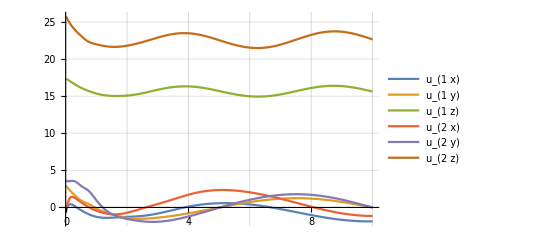
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=inputList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[1],aux[2],aux[3],
aux[4],aux[5],aux[6]
},
PlotLegends->Placed[{"u_(1  x)","u_(1  y)","u_(1  z)","u_(2  x)","u_(2  y)","u_(2  z)"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures_no_attitude/sim_input.pdf",%];
```

## Tensions

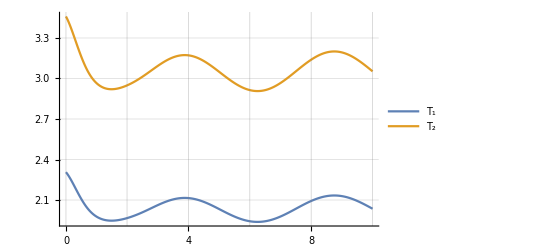
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=tensionsList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[1],
aux[2]
},
PlotLegends->Placed[{"T_1","T_2"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures_no_attitude/sim_tensions.pdf",%];
```

# Attitude Control

## Generate a point in augmented state space

```mathematica
zal[l_]:=Join[zl[l[[1;;14]]],uv3[l[[15;;16]]],uv3[l[[17;;18]]]]
zalR[]=zal[RandomReal[{-1,1},22]];
(*Timing[Zp[0.1,zalR[]]]*)
```

## Augmented vector field

```mathematica
Za[za_,{U1_,U2_,ω1_,ω2_}]:=Join[
Z[za[[1;;18]],Join[U1 r1[za] ,U2 r2[za] ]],
Skew[ω1].r1[za],
Skew[ω2].r2[za]
]
```

## UAVs attitude

```mathematica
r1[za_]:=za[[19;;21]]
r2[za_]:=za[[22;;24]]
```

## Chosen throttle control laws

```mathematica
U1cl[za_,ucl_] := (n1[za[[1;;9]]].ucl[[1;;3]])/(n1[za[[1;;9]]].r1[za])/.PhysicalConstants
U2cl[za_,ucl_] := (n2[za[[1;;9]]].ucl[[4;;6]])/(n2[za[[1;;9]]].r2[za])/.PhysicalConstants
Ucl[za_,ucl_]:=Join[U1cl[za,ucl]r1[za] ,U2cl[za,ucl]r2[za] ]

Uclaux[t_,za_]:=Join[U1cl[za,#]r1[za] ,U2cl[za,#]r2[za] ]&[ucl[t,za[[1;;18]]]]
```

## Vector field Z with chosen throttle control laws

```mathematica
Zp[t_,za_]:=Z[za[[1;;18]],Ucl[za,ucl[t,za[[1;;18]]]]]
```

## Error in dynamics for chosen throttle control laws

```mathematica
ClosedLoopIdealDynamics[t_,zz_]:=Join[
zz[[10;;12]],
v1cl[t,g[zz[[1;;18]]][[1;;12]]][[1]] nT[zz[[1;;9]]] - gravity{0,0,1},
Skew[ωT[zz[[1;;9]],zz[[10;;18]]]].nT[zz[[1;;9]]],
OP[nT[zz[[1;;9]]]].v1cl[t,g[zz[[1;;18]]][[1;;12]]][[2]],
{ωθ[zz[[1;;9]],zz[[10;;18]]],uθcl[zz[[1;;18]]]},
{ωψ[zz[[1;;9]],zz[[10;;18]]],uψcl[zz[[1;;18]]]}
]/.PhysicalConstants
(*error is proportional to Skew[ri] uicl*)
ErrorDynamicsDueToUAVsAttitude[t_,zz_]:=Join[
{0,0,0},
{0,0,0},
{0,0,0},
BτNT[zz[[1;;9]]].#,
{0,Bθ[zz[[1;;9]]].#},
{0,Bψ[zz[[1;;9]]].#}
]&[Join[(Skew[n1[zz[[1;;9]]]].Skew[r1[zz]].(ucl[t,zz[[1;;18]]][[1;;3]]))/(n1[zz[[1;;9]]].r1[zz]),(Skew[n2[zz[[1;;9]]]].Skew[r2[zz]].(ucl[t,zz[[1;;18]]][[4;;6]]))/(n2[zz[[1;;9]]].r2[zz])]
]/.PhysicalConstants
DynamicsEquality[t_,zz_]:=(D[g[z],{z}]/.Thread[z-> zz[[1;;18]]]).Zp[t,zz]-(ClosedLoopIdealDynamics[t,zz]+ErrorDynamicsDueToUAVsAttitude[t,zz])/.PhysicalConstants
Chop[DynamicsEquality[0.1,zalR[]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Time derivative of desired input

```mathematica
(*slow option*)
(*d1ucl[t_,za_]:=D[ucl[τ,z],Join[{τ},z]].Join[{1},Zp[t,za] ]/.{τ-> t}/.Thread[z-> za[[1;;18]]]*)
d1ucl[t_,za_]:=(ucl[t+#dt,za[[1;;18]]+#dt Zp[t,za]]-ucl[t,za[[1;;18]]])/(#dt)&[<|"dt"->  0.001|>]
Timing[d1ucl[0.1,zalR[]]]
```

{0.64,{230.674,18.1605,-669.342,255.425,-164.601,-204.79}}

## Control laws for UAVs angular velocities

```mathematica
ωr[r_,u_,du_]:=Skew[u/(√(u.u))].(du/(√(u.u)))+kθAttitude Skew[r].(u/(√(u.u)))/.{kθAttitude-> 2.5}
```

## Complete control law

```mathematica
uacl[t_,za_]:={
U1cl[za,#]/.PhysicalConstants,
U2cl[za,#]/.PhysicalConstants,
ωr[r1[za],#1[[1;;3]],#2[[1;;3]]],
ωr[r2[za],#1[[4;;6]],#2[[4;;6]]]
}&[ucl[t,za[[1;;18]]],d1ucl[t,za]]
zarandom=zalR[];
Timing[uacl[0.1,zarandom]]
```

{0.864,{187.785,163.723,{-10.8372,27.1685,-2.48101},{9.56097,11.19,0.663095}}}

## Closed loop vector field

```mathematica
Zacl[t_,za_]:=Za[za,uacl[t,za]]
zarandom=zalR[];
Timing[Zacl[0.1,zarandom]]
```

{0.832,{-0.250225,-0.497597,0.845517,-0.469942,-0.517114,1.05677,-0.385571,-0.476293,0.881596,3.14348,-0.453046,-0.997046,-35.6087,-53.158,107.983,-6.2532,61.9875,42.9757,23.0879,10.2362,11.2426,6.93473,-6.39549,7.93688}}

## Initial condition

```mathematica
(*use previous initial condition*)
z0=Join[{0,0,0},L1 uv3[{-0.1,-0.2}],L2 uv3[{0.2,0.4}],{0,0,0},{0,0,0},{0,0,0}]/.PhysicalConstants;
z0=Join[z0,uv3[{0,0}],uv3[{0,0}]]/.PhysicalConstants;
```

## Project any point in R24 to augmented state space

```mathematica
Proja[za_]:=Join[
Proj[za[[1;;18]]],
#/(√(#.#))&[r1[za]],
#/(√(#.#))&[r2[za]]
]/.PhysicalConstants;
Chop[#-Proja[#]&[zalR[]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Simulation

```mathematica
stepsize=0.01;
NN=1000;

stateList={};
rstarList={};
inputList ={};
tensionsList={};
kk=1;

For[i=1,i<=NN,i++,
time=stepsize(i-1);
input =uacl[time,z0];
tensions= Tensions[z0[[1;;18]],Uclaux[time,z0]]/.PhysicalConstants;

stateList= Join[stateList,{z0}];
rstarList= Join[rstarList,{Join[(#[[1;;3]])/(√(#[[1;;3]].#[[1;;3]])),(#[[4;;6]])/(√(#[[4;;6]].#[[4;;6]]))]&[ucl[time,z0[[1;;18]]]]}];
inputList= Join[inputList,{input}];
tensionsList = Join[tensionsList,{tensions}];

zdot=  Za[z0,input]/.PhysicalConstants;
z0=Proja[z0+stepsize zdot]/.PhysicalConstants;

If[i≥100 kk,Beep[];Print[i];kk=kk+1];
]
```

100

200

300

400

500

600

700

800

900

1000

```mathematica
(*NN=Length[stateList]*)
```

## export

```mathematica
Export[NotebookDirectory[]<>"figures/matlab/data_state.mat",stateList];
Export[NotebookDirectory[]<>"data_state.mx",stateList];
Export[NotebookDirectory[]<>"data_input.mx",inputList];
Export[NotebookDirectory[]<>"data_tensions.mx",tensionsList];

(*stateList=Import[NotebookDirectory[]<>"data_state.mx"];
input3dList=Import[NotebookDirectory[]<>"data_input.mx"];
tensionsList=Import[NotebookDirectory[]<>"data_tensions.mx"];*)
```

## Error position

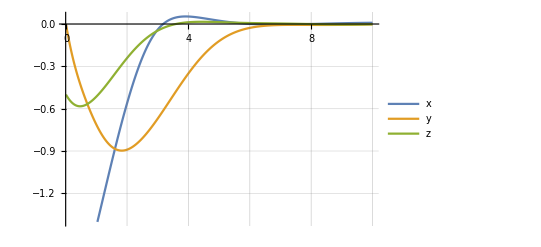
-Graphics-time (s)error(m)

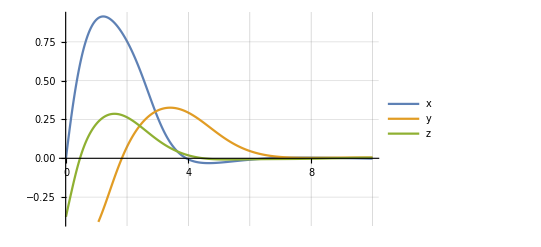
-Graphics-time (s)error(m)

```mathematica
errorp=stateList[[1;;NN,{1,2,3}]]-Table[pd[stepsize(i-1)],{i,1,NN}];
Labeled[
ListLinePlot[{
errorp[[;;,1]],
errorp[[;;,2]],
errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m)"},{Bottom,Left},RotateLabel->True
]

errorv=stateList[[1;;NN,{10,11,12}]]-Table[pd'[stepsize(i-1)],{i,1,NN}];
Labeled[
ListLinePlot[{
errorv[[;;,1]],
errorv[[;;,2]],
errorv[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/sim_error_position.pdf",%];
```

## Error attitude

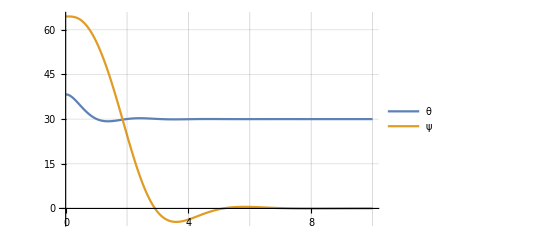
-Graphics-time (s)error(deg)

```mathematica
Labeled[
ListLinePlot[{
Table[θ[stateList[[i]][[1;;9]]] 180/π/.PhysicalConstants,{i,1,NN}],
Table[ψ[stateList[[i]][[1;;9]]] 180/π/.PhysicalConstants,{i,1,NN}]
(*Table[ωθ[stateList[[i]][[1;;9]],stateList[[i]][[10;;18]]] 180/π/.PhysicalConstants,{i,1,NN}],*)
(*Table[(ArcTan[{1,0,0}.nH[#],{0,1,0}.nH[#]]&[stateList[[i]][[1;;9]]] )180/π/.PhysicalConstants,{i,1,NN}]*)
},
PlotLegends->Placed[{"θ","ψ"},Above],
Ticks-> {XTicksLabels,Automatic},
PlotRange->Automatic,
GridLines->Automatic
],
{"time (s)","error(deg)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/sim_error_attitude.pdf",%];
```

## Input

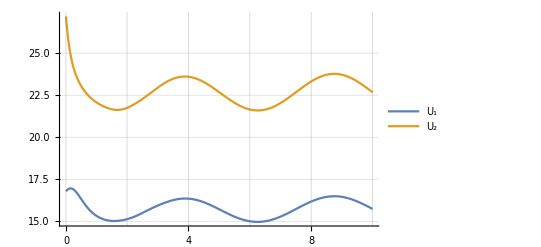
-Graphics-time (s)Thrust(N)

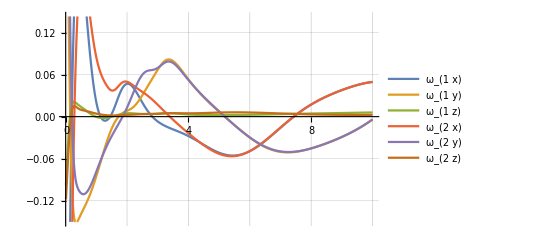
-Graphics-time (s)angular velocity(hz)

```mathematica
aux[comp_]:=inputList[[;;]][[comp]]
Labeled[
ListLinePlot[{
Table[inputList[[i]][[1]],{i,1,NN}],
Table[inputList[[i]][[2]],{i,1,NN}]
},
PlotLegends->Placed[{"U_1","U_2"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","Thrust(N)"},{Bottom,Left},RotateLabel->True
]
Export[NotebookDirectory[]<>"figures/sim_uavs_thrusts.pdf",%];
aux[comp_]:=inputList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
Table[inputList[[i]][[3]][[1]],{i,1,NN}],
Table[inputList[[i]][[3]][[2]],{i,1,NN}],
Table[inputList[[i]][[3]][[3]],{i,1,NN}],
Table[inputList[[i]][[4]][[1]],{i,1,NN}],
Table[inputList[[i]][[4]][[2]],{i,1,NN}],
Table[inputList[[i]][[4]][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"ω_(1  x)","ω_(1  y)","ω_(1  z)","ω_(2  x)","ω_(2  y)","ω_(2  z)"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","angular velocity(hz)"},{Bottom,Left},RotateLabel->True
]
Export[NotebookDirectory[]<>"figures/sim_uavs_angular_velocities.pdf",%];
```

## Error attitude in UAV

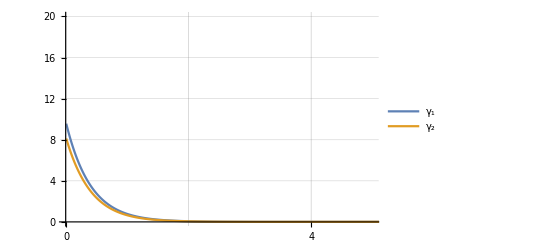
-Graphics-time (s)error(deg)

```mathematica
Labeled[
ListLinePlot[{
Table[ArcCos[r1[stateList[[i]]].rstarList[[i]][[1;;3]]] 180/π/.PhysicalConstants,{i,1,NN}],
Table[ArcCos[r2[stateList[[i]]].rstarList[[i]][[4;;6]]] 180/π/.PhysicalConstants,{i,1,NN}]
},
PlotLegends->Placed[{"γ_1","γ_2"},Above],
Ticks-> {XTicksLabels,Automatic},
PlotRange->{{0,5/stepsize},{0,20}},
GridLines->Automatic
],
{"time (s)","error(deg)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/sim_uavs_attitude_error.pdf",%];
```

## Tensions

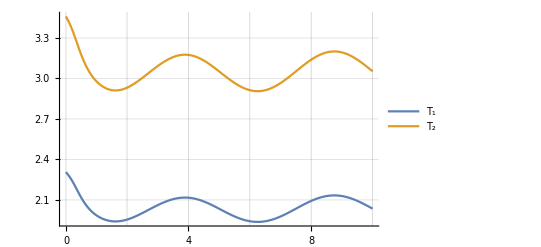
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=tensionsList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[1],
aux[2]
},
PlotLegends->Placed[{"T_1","T_2"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/sim_tensions.pdf",%];
```

# Appendix: details in obtaining explicit ubar

## Some details in obtaining explicit ubar (“inverting RB”)

### first controlling the tensions: determines component along n1 and n2

```mathematica
equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=
(m T)/(√(NT[zk].NT[zk])){ w1 ,w2}-Tensions[z,Join[u1x n1[zk],u2x n2[zk]]]/.Thread[{u1x,u2x}-> DiagonalMatrix[{m1/m,m2/m}].MT[zk].((m T)/(√(NT[zk].NT[zk])){ w1 ,w2}-Tensions[z,{0,0,0,0,0,0}])]/.
PhysicalConstants;
Chop[equality[#1,#2]&[zlR[],{1,2,3,4,5,6}]]
```

{0,0}

```mathematica
(*equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{u1x_,u1y_,u1z_,u2x_,u2y_,u2z_}]=
1/(√(NT[zk].NT[zk]))Skew[nT[zk]].(w1/L1(({u1x,u1y,u1z}- n1[zk] T1U[zk].{u1x,u1y,u1z,u2x,u2y,u2z})/m1-(n1[zk] T1U[zk].{u1x,u1y,u1z,u2x,u2y,u2z}+  n2[zk] T2U[zk].{u1x,u1y,u1z,u2x,u2y,u2z})/m)+w2/L2(({u2x,u2y,u2z}- n2[zk] T2U[zk].{u1x,u1y,u1z,u2x,u2y,u2z})/m2-(n1[zk] T1U[zk].{u1x,u1y,u1z,u2x,u2y,u2z}+  n2[zk] T2U[zk].{u1x,u1y,u1z,u2x,u2y,u2z})/m))-BτNT[zk].{u1x,u1y,u1z,u2x,u2y,u2z}/.PhysicalConstants;*)

(*equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=
1/(√(NT[zk].NT[zk]))Skew[nT[zk]].(w1/L1((u1x n1[zk]- n1[zk](m T)/(√(NT[zk].NT[zk]))w1)/m1-(n1[zk] (m T)/(√(NT[zk].NT[zk]))w1+  n2[zk] (m T)/(√(NT[zk].NT[zk]))w2)/m)+w2/L2((u2x n2[zk]- n2[zk] (m T)/(√(NT[zk].NT[zk]))w2)/m2-(n1[zk] (m T)/(√(NT[zk].NT[zk]))w1+  n2[zk] (m T)/(√(NT[zk].NT[zk]))w2)/m))-BτNT[zk].Join[u1x n1[zk],u2x n2[zk]]/.
Thread[{u1x,u2x}-> DiagonalMatrix[{m1/m,m2/m}].MT[zk].((m T)/(√(NT[zk].NT[zk])){ w1 ,w2}-Tensions[z,{0,0,0,0,0,0}])]/.PhysicalConstants;*)
```

## first step

```mathematica
ubar1st[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},T_]=Join[u1x n1[zk],u2x n2[zk]]/.Thread[{u1x,u2x}-> DiagonalMatrix[{m1/m,m2/m}].MT[zk].((m T)/(√(NT[zk].NT[zk])){ w1 ,w2}-Tensions[z,{0,0,0,0,0,0}])]/.PhysicalConstants;

Chop[
Join[m #2[[1]] nT[#1[[1;;9]]],OP[nT[#1[[1;;9]]]].{#2[[2]],#2[[3]],#2[[4]]},{#2[[5]],#2[[6]]}]-
(RA[#1]+RB[#1[[1;;9]]].ubar1st[#1,#2[[1]]]) &[zlR[],RandomReal[{-10,10},{6}]]/.PhysicalConstants
]
```

{-2.15309,0.522311,-2.99436,6.32939,-6.36804,-5.66194,-17.4122,-6.84454}

### Next: determine components along S[n1].nT and Skew[n2].nT so as to control torque of nT (along direction OP[nT].n1)

#### Idea: τNT = BτNT.u + AτNT BτNT[zk] . [ ? S[n1].nT, ? S[n2].nT] τNT = Skew[nT].1/Norm[NT](w1 A1/L1+w2 A2/L2)

```mathematica
equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=
Skew[nT[zk]].( #1/(√(#1.#1))-#2/(√(#2.#2)))-BτNT[zk].Join[(L1 m1)/w1 √(NT[zk].NT[zk]) #1/(√(#1.#1)),-(L2 m2)/w2 √(NT[zk].NT[zk])#2/(√(#2.#2))]&[Skew[n1[zk]].nT[zk],Skew[n2[zk]].nT[zk]]/.PhysicalConstants;
Chop[equality[#1,#2]&[zlR[],{0,0,0,0,0,0}]]
equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=
(OP[nT[zk]].n1[zk])/(√(#1.#1))-BτNT[zk].Join[(L1 m1)/w1 √(NT[zk].NT[zk])1/2 #1/(√(#1.#1)),-(L2 m2)/w2 √(NT[zk].NT[zk])1/2#2/(√(#2.#2))]&[Skew[n1[zk]].nT[zk],Skew[n2[zk]].nT[zk]]/.PhysicalConstants;
Chop[equality[#1,#2]&[zlR[],{0,0,0,0,0,0}]]
```

{0,0,0}

{0,0,0}

### null space (used to control yaw)

```mathematica
equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=
BτNT[zk].Join[(L1 m1)/w1 √(NT[zk].NT[zk]) #1/(√(#1.#1)),(L2 m2)/w2 √(NT[zk].NT[zk])#2/(√(#2.#2))]&[Skew[n1[zk]].nT[zk],Skew[n2[zk]].nT[zk]]/.PhysicalConstants;
Chop[equality[#1,#2]&[zlR[],{0,0,0,0,0,0}]]
```

{0,0,0}

### Next: determine components along OP[n1].nT and OP[n2].nT so as to control torque of nT (along direction sk[nT].n1) (Note that u1,Skew[n1].nT , OP[n1].nT forms a basis for uav 1)

#### Idea: τNT = BτNT.u + AτNT BτNT[zk] . [ ? OP[n1].nT, ? OP[n2].nT] τNT = Skew[nT].1/Norm[NT](w1 A1/L1+w2 A2/L2)

```mathematica
equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=
1/(√(NT[zk].NT[zk]))Skew[nT[zk]].( w1/L1 1/m1#1/(√(#1.#1))+w2/L2 1/m2#2/(√(#2.#2)))-BτNT[zk].Join[#1/(√(#1.#1)),#2/(√(#2.#2))]&[OP[n1[zk]].nT[zk],OP[n2[zk]].nT[zk]]/.PhysicalConstants;
Chop[equality[#1,#2]&[zlR[],{0,0,0,0,0,0}]]

equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=
Skew[nT[zk]].(#1/(√(#1.#1))-#2/(√(#2.#2)))-BτNT[zk].Join[(L1 m1)/w1 √(NT[zk].NT[zk])#1/(√(#1.#1)),-(L2 m2)/w2 √(NT[zk].NT[zk])#2/(√(#2.#2))]&[OP[n1[zk]].nT[zk],OP[n2[zk]].nT[zk]]/.PhysicalConstants;
Chop[equality[#1,#2]&[zlR[],{0,0,0,0,0,0}]]

equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=
((#/(√(#.#))&)[Skew[nT[zk]].n2[zk]](n1[zk].nT[zk]+n2[zk].nT[zk]))-BτNT[zk].Join[(L1 m1)/w1 √(NT[zk].NT[zk])#1/(√(#1.#1)),-(L2 m2)/w2 √(NT[zk].NT[zk])#2/(√(#2.#2))]&[OP[n1[zk]].nT[zk],OP[n2[zk]].nT[zk]]/.PhysicalConstants;
Chop[equality[#1,#2]&[zlR[],{0,0,0,0,0,0}]]
equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=
((#/(√(#.#))&)[Skew[nT[zk]].n2[zk]])-BτNT[zk].Join[((L1 m1)/w1 √(NT[zk].NT[zk]))/(n1[zk].nT[zk]+n2[zk].nT[zk])#1/(√(#1.#1)),-((L2 m2)/w2 √(NT[zk].NT[zk]))/(n1[zk].nT[zk]+n2[zk].nT[zk])#2/(√(#2.#2))]&[OP[n1[zk]].nT[zk],OP[n2[zk]].nT[zk]]/.PhysicalConstants;
Chop[equality[#1,#2]&[zlR[],{0,0,0,0,0,0}]]

equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=
((#/(√(#.#))&)[Skew[nT[zk]].n1[zk]])-BτNT[zk].Join[-((L1 m1)/w1 √(NT[zk].NT[zk]))/(n1[zk].nT[zk]+n2[zk].nT[zk])#1/(√(#1.#1)),((L2 m2)/w2 √(NT[zk].NT[zk]))/(n1[zk].nT[zk]+n2[zk].nT[zk])#2/(√(#2.#2))]&[OP[n1[zk]].nT[zk],OP[n2[zk]].nT[zk]]/.PhysicalConstants;
Chop[equality[#1,#2]&[zlR[],{0,0,0,0,0,0}]]
```

{0,0,0}

{0,0,0}

{0,0,0}

«2 more identical outputs»

### null space (used to control theta)

```mathematica
equality[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=BτNT[zk].Join[-((L1 m1)/w1 √(NT[zk].NT[zk]))/(n1[zk].nT[zk]+n2[zk].nT[zk])1/(n1[zk].nT[zk])#1/(√(#1.#1)),((L2 m2)/w2 √(NT[zk].NT[zk]))/(n1[zk].nT[zk]+n2[zk].nT[zk])-1/(n2[zk].nT[zk])#2/(√(#2.#2))]&[OP[n1[zk]].nT[zk],OP[n2[zk]].nT[zk]]/.PhysicalConstants;
Chop[equality[#1,#2]&[zlR[],{0,0,0,0,0,0}]]
```

{0,0,0}

## second step

```mathematica
uv=#/(√(#.#))&;
```

```mathematica
(*ubar2nd[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=ubar1st[z,T]+Join[
((L1 m1)/w1(τψ+√(NT[zk].NT[zk])1/2{ττx,ττy,ττz}.uv[OP[nT[zk]].n1[zk]])#1/(√(#1.#1))-(L1 m1)/w1(1/(n1[zk].nT[zk])τθ+(√(NT[zk].NT[zk]))/(n1[zk].nT[zk]+n2[zk].nT[zk]){ττx,ττy,ττz}.uv[Skew[nT[zk]].n1[zk]])#2/(√(#2.#2)))&[Skew[n1[zk]].nT[zk],OP[n1[zk]].nT[zk]],
((L2 m2)/w2(τψ+√(NT[zk].NT[zk])1/2{ττx,ττy,ττz}.uv[OP[nT[zk]].n2[zk]])#1/(√(#1.#1))-(L2 m2)/w2(1/(n2[zk].nT[zk])τθ+(√(NT[zk].NT[zk]))/(n1[zk].nT[zk]+n2[zk].nT[zk]){ττx,ττy,ττz}.uv[Skew[nT[zk]].n2[zk]])#2/(√(#2.#2)))&[Skew[n2[zk]].nT[zk],OP[n2[zk]].nT[zk]]
]/.Thread[{ττx,ττy,ττz}-> {τx,τy,τz}-(AτNT[z]+BτNT[zk].ubar1st[z,T]) ]/.PhysicalConstants;*)
ubar2nd[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=ubar1st[z,T]+Join[
((L1 m1)/w1(τψ+√(NT[zk].NT[zk])1/2{ττx,ττy,ττz}.uv[OP[nT[zk]].n1[zk]])#1/(√(#1.#1))-(L1 m1)/w1(1/(n1[zk].nT[zk])τθ+(NT[zk].NT[zk])/((w1 +w2)(1+ n1[zk].n2[zk])){ττx,ττy,ττz}.uv[Skew[nT[zk]].n1[zk]])#2/(√(#2.#2)))&[Skew[n1[zk]].nT[zk],OP[n1[zk]].nT[zk]],
((L2 m2)/w2(τψ+√(NT[zk].NT[zk])1/2{ττx,ττy,ττz}.uv[OP[nT[zk]].n2[zk]])#1/(√(#1.#1))-(L2 m2)/w2(1/(n2[zk].nT[zk])τθ+(NT[zk].NT[zk])/((w1 +w2)(1+ n1[zk].n2[zk])){ττx,ττy,ττz}.uv[Skew[nT[zk]].n2[zk]])#2/(√(#2.#2)))&[Skew[n2[zk]].nT[zk],OP[n2[zk]].nT[zk]]
]/.Thread[{ττx,ττy,ττz}-> {τx,τy,τz}-(AτNT[z]+BτNT[zk].ubar1st[z,T]) ]/.PhysicalConstants;

(*now torque of thrust vector is also controlled: missing the theta  and yaw control*)
Chop[
Join[m #2[[1]] nT[#1[[1;;9]]],OP[nT[#1[[1;;9]]]].{#2[[2]],#2[[3]],#2[[4]]},{#2[[5]],#2[[6]]}]-
(RA[#1]+RB[#1[[1;;9]]].ubar2nd[#1,#2]) &[zlR[],{0.1,0.2,1,2,2,0}]/.PhysicalConstants
]
```

{-0.0106415,-0.0115737,-0.0474638,0,0,0,-11.6662,0.439759}

## check equality (simplification above)

```mathematica
zrandom=zlR[];
test1=(√(NT[zk].NT[zk]))/(n1[zk].nT[zk]+n2[zk].nT[zk]);
(*test2=(NT[zk].NT[zk])/((w1 +w2 n1[zk].n2[zk])+(w2+w1 n1[zk].n2[zk]));*)
test2=(NT[zk].NT[zk])/((w1 +w2)(1+ n1[zk].n2[zk]));
Chop[Simplify[test1-test2/.Thread[zk->zrandom[[1;;9]]]/.PhysicalConstants]]
```

0

## θ control θ=arccos(n1.n2) θ̇=-1/(√(1-(n1.n2)^2))(n1dot.n2+n1.n2dot) θ^(..)=-1/(√(1-(n1.n2)^2))(n1ddot.n2+n1.n2ddot)+... θ^(..)=-1/(√(1-(n1.n2)^2))(A1/L1.n2+n1.A2/L)+... θ^(..)=-1/(√(1-(n1.n2)^2))((OP[n1].nT)/L1.n2+n1.(OP[n2].nT)/L)+... (components (OP[n1].nT)/L1.n2 and (OP[n2].nT)/L2.n1 do not affect yaw! Important)

```mathematica
(*ubar3rd[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=ubar2nd[z,{T,τx,τy,τz,ττθ,τψ}]/.{ττθ-> (√(1-(n1[zk].n2[zk])^2))/((n2[zk].uv[OP[n1[zk]].nT[zk]])/(w1 n1[zk].nT[zk])+(n1[zk].uv[OP[n2[zk]].nT[zk]])/(w2  n2[zk].nT[zk]))(τθ-(Aθ[z]+Bθ[zk].ubar2nd[z,{T,τx,τy,τz,0,0}]))}/.PhysicalConstants;*)
ubar3rd[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=ubar2nd[z,{T,τx,τy,τz,ττθ,τψ}]/.{ττθ-> ((w2^2 + w1 w2 n1[zk].n2[zk])(w1^2 +w1 w2 n1[zk].n2[zk]))/(√(NT[zk].NT[zk]))^3(τθ-(Aθ[z]+Bθ[zk].ubar2nd[z,{T,τx,τy,τz,0,0}]))}/.PhysicalConstants;
(*now theta is also controlled: missing the yaw*)
Chop[
Join[m #2[[1]] nT[#1[[1;;9]]],OP[nT[#1[[1;;9]]]].{#2[[2]],#2[[3]],#2[[4]]},{#2[[5]],#2[[6]]}]-
(RA[#1]+RB[#1[[1;;9]]].ubar3rd[#1,#2]) &[zrandom,{0.1,0.2,1,2,2,0}]/.PhysicalConstants
]
```

{-0.0121291,0.0360798,-0.0324212,0,0,0,0,-1.00291}

#### check equality (simplification above)

```mathematica
zrandom=zlR[];
test1=((n2[zk].uv[OP[n1[zk]].nT[zk]])/(w1 n1[zk].nT[zk])+(n1[zk].uv[OP[n2[zk]].nT[zk]])/(w2  n2[zk].nT[zk]));
(*test2=(w2(n2[zk].OP[n1[zk]].n2[zk])/(w1 n1[zk].nT[zk])1/(√(#.#&[OP[n1[zk]].nT[zk]]))+w1(n1[zk].OP[n2[zk]].n1[zk])/(w2  n2[zk].nT[zk])1/(√(#.#&[OP[n2[zk]].nT[zk]])))1/(√(NT[zk].NT[zk]));*)
(*test2=(w2(1-(n1[zk].n2[zk])^2)/(w1 n1[zk].nT[zk])1/(√(#.#&[OP[n1[zk]].nT[zk]]))+w1(1-(n1[zk].n2[zk])^2)/(w2  n2[zk].nT[zk])1/(√(#.#&[OP[n2[zk]].nT[zk]])))1/(√(NT[zk].NT[zk]));*)
(*test2=(w2(1-(n1[zk].n2[zk])^2)/(w1 n1[zk].nT[zk])1/(√(w2^2(1-(n1[zk].n2[zk])^2)))+w1(1-(n1[zk].n2[zk])^2)/(w2  n2[zk].nT[zk])1/(√(w1^2(1-(n1[zk].n2[zk])^2))));*)
(*test2=((√(1-(n1[zk].n2[zk])^2))/(w1 n1[zk].nT[zk])+(√(1-(n1[zk].n2[zk])^2))/(w2  n2[zk].nT[zk]));*)
(*test2=√(1-(n1[zk].n2[zk])^2)(1/(w1 (w1 +w2 n1[zk].n2[zk]))+1/(w2 (w2 + w1 n1[zk].n2[zk])))√(NT[zk].NT[zk]);*)
(*test2=√(1-(n1[zk].n2[zk])^2)((w1^2+w2^2 + 2w1 w2 n1[zk].n2[zk])/((w1^2 +w1 w2 n1[zk].n2[zk]) (w2^2 + w1 w2 n1[zk].n2[zk])))√(NT[zk].NT[zk]);*)
(*test2=√(1-(n1[zk].n2[zk])^2)(((w1+w2)^2 + 2w1 w2(n1[zk].n2[zk]-1))/((w1^2 +w1 w2 n1[zk].n2[zk]) (w2^2 + w1 w2 n1[zk].n2[zk])))√(NT[zk].NT[zk]);*)
test2=√(1-(n1[zk].n2[zk])^2)((√(NT[zk].NT[zk]))^3/((w1^2 +w1 w2 n1[zk].n2[zk]) (w2^2 + w1 w2 n1[zk].n2[zk])));

Chop[Simplify[test1-test2/.Thread[zk->zrandom[[1;;9]]]/.PhysicalConstants]]
```

0

## ψ control: Only components along OP[n1].nT and OP[n2].nT left! ψ=1/2 arctan((e1.nH)^2-(e2.nH)^2 ,2e1.nH e2.nH) ψ̇=(e2.nH e1.nHdot-e1.nH e2.nHdot) ψ^(..)=(-e2.nH e1.nHddot+e1.nH e2.nHddot)+... ψ^(..)=(-e2.nH e1.(OP[e3].(n^(..)1-n^(..)2))/(...)+e1.nH e2.(OP[e3].(n^(..)1-n^(..)2))/(...))+... ψ^(..)=(-e2.nH e1.(OP[e3].(?(OP[n1].nT)-?OP[n2].nT))/(...)+e1.nH e2.(OP[e3].(?(OP[n1].nT)-?OP[n2].nT))/(...))+... easier to check this yaw, but there is some equilavence that needs to be taken care because arctan(e1.nH ,e2.nH)’’=’’1/2 arcsin(2 e1.nH e2.nH)

```mathematica
D[1/2 ArcTan[x^2-y^2 ,2 x y],{{x,y}}].{xd,yd}//Simplify
D[ArcTan[x ,y],{{x,y}}].{xd,yd}//Simplify
D[1/2 ArcTan[x^2-y^2 ,2 x y],{{x,y}}].{xd,yd}/.{x-> Cos[γ],y-> Sin[γ]}//Simplify
D[ArcTan[x ,y],{{x,y}}].{xd,yd}/.{x-> Cos[γ],y-> Sin[γ]}//Simplify
D[1/2 ArcTan[x^2-y^2 ,2 x y],{{x,y}}].{xd,yd}/.{x-> Cos[γ],y-> Sin[γ],xd-> -Sin[γ]γd,yd-> Cos[γ]γd}//Simplify
D[ArcTan[x ,y],{{x,y}}].{xd,yd}/.{x-> Cos[γ],y-> Sin[γ],xd-> -Sin[γ]γd,yd-> Cos[γ]γd}//Simplify
```

(-xd y+x yd)/(x^2+y^2)

(-xd y+x yd)/(x^2+y^2)

yd Cos[γ]-xd Sin[γ]

yd Cos[γ]-xd Sin[γ]

γd

γd

```mathematica
(*this is what we get with ψ=arctan(e1.nH,e2.nH): but there is the sign *)
ubar4th[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_},{T_,τx_,τy_,τz_,τθ_,τψ_}]=ubar3rd[z,{T,τx,τy,τz,τθ,ττψ}]/.{ττψ->(NH[zk].NH[zk] √(1-(n1[zk].n2[zk])^2))/((1/w1+1/w2)({0,0,1}.n1[zk]+{0,0,1}.n2[zk])(n1[zk].n2[zk]-1))(τψ-(Aψ[z]+Bψ[zk].ubar3rd[z,{T,τx,τy,τz,τθ,0}]))}/.PhysicalConstants;
```

```mathematica
(*now theta is also controlled: missing the yaw*)
Chop[
Join[m #2[[1]] nT[#1[[1;;9]]],OP[nT[#1[[1;;9]]]].{#2[[2]],#2[[3]],#2[[4]]},{#2[[5]],#2[[6]]}]-
(RA[#1]+RB[#1[[1;;9]]].ubar4th[#1,#2]) &[zrandom,{0.1,0.2,1,2,2,0}]/.PhysicalConstants
]
```

{0.0106464,0.0207147,-0.0442443,0,0,0,0,0}

some interesting things to note

```mathematica
zd
```

{vx,vy,vz,v1x,v1y,v1z,v2x,v2y,v2z}

```mathematica
zrandom=zlR[];
ψ1[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=1/2 ArcTan[({1,0,0}.nH[zk])^2-({0,1,0}.nH[zk])^2,2({1,0,0}.nH[zk])({0,1,0}.nH[zk])];
ωψ1[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_},{vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=vf[ψ1][zk,zd];
Bψ1[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Bf[ψ1][zk];
Aψ1[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Af[ψ1][z];



ψ2[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=ArcTan[{1,0,0}.nH[zk],{0,1,0}.nH[zk]];
ωψ2[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_},{vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=vf[ψ2][zk,zd];
Bψ2[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_}]=Bf[ψ2][zk];
Aψ2[{px_,py_,pz_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_,vx_,vy_,vz_,v1x_,v1y_,v1z_,v2x_,v2y_,v2z_}]=Af[ψ2][z];

(ψ1[zrandom[[1;;9]]]-ψ2[zrandom[[1;;9]]])/(π/4)
Chop[ωψ1[#[[1;;9]],#[[10;;18]]]- ωψ2[#[[1;;9]],#[[10;;18]]]&[zrandom]]
Chop[Bψ1[zrandom[[1;;9]]]-  Bψ2[zrandom[[1;;9]]]]
Chop[Aψ1[zrandom]-Aψ2[zrandom]]
```

-4.

0

{0,0,0,0,0,0}

0

## check equality (simplify when ψ=arctan(e1.nH ,e2.nH))

```mathematica
Thread[zk->zrandom[[1;;9]]]
```

{px→0.749797,py→-0.739151,pz→-0.611337,p1x→0.71827,p1y→-0.785135,p1z→-0.114456,p2x→0.983497,p2y→-0.928521,p2z→0.0207414}

```mathematica
test1=({1,0,0}.nH[zk] {0,1,0}-{0,1,0}.nH[zk] {1,0,0}).OP[nH[zk]].uv[Skew[n1[zk]].nT[zk]];
(*test2={0,0,1}.Skew[nH[zk]].uv[Skew[n1[zk]].nT[zk]]&[ Skew[n1[zk]].nT[zk],NT[zk]];*)
(*test2={0,0,1}.Skew[nH[zk]].Skew[n1[zk]].n2[zk] 1/(√(#1.#1))w2/(√(#2.#2))&[ Skew[n1[zk]].nT[zk],NT[zk]];*)
(*test2={0,0,1}.(n1[zk](nH[zk].n2[zk]) -n2[zk](nH[zk].n1[zk]) )1/(√(#1.#1))w2/(√(#2.#2))&[ Skew[n1[zk]].nT[zk],NT[zk]];*)
(*test2=({0,0,1}.n1[zk](n1[zk]-n2[zk])/(√(NH[zk].NH[zk])).n2[zk] -{0,0,1}.n2[zk](n1[zk]-n2[zk])/(√(NH[zk].NH[zk])).n1[zk] )1/(√(#1.#1))w2/(√(#2.#2))&[ Skew[n1[zk]].nT[zk],NT[zk]];*)
test2=({0,0,1}.n1[zk]+{0,0,1}.n2[zk])(n1[zk].n2[zk]-1)/(√(NH[zk].NH[zk])) 1/(√(#1.#1))w2/(√(#2.#2))&[ Skew[n1[zk]].nT[zk],NT[zk]];
Chop[Simplify[test1-test2/.Thread[zk->zrandom[[1;;9]]]/.PhysicalConstants]]
```

0

#### some interesting: vector plot for yaw dynamics (check that bar orientation does not ‘see’ 180 degree difference)

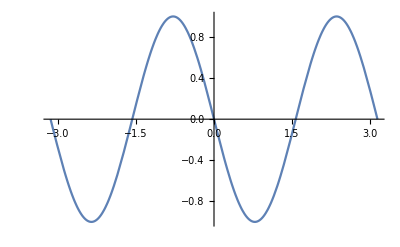

```mathematica
Plot[-Sin[2 1/2 ArcTan[Cos[γ]^2-Sin[γ]^2,2 Sin[γ]Cos[γ]]],{γ,-π,π}]
```

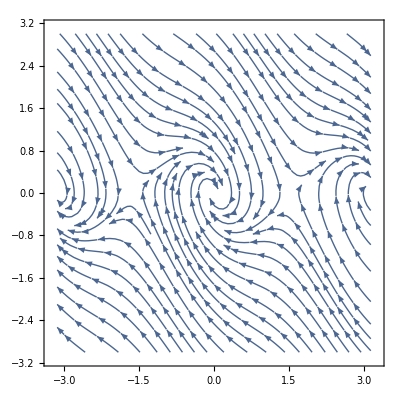

```mathematica
StreamPlot[{vv,-Sin[2 1/2 ArcTan[Cos[γ]^2-Sin[γ]^2,2 Sin[γ]Cos[γ]]]-vv},{γ,-π,π},{vv,-3,3}]
```